```mathematica
Needs["Constants`"]
Needs["Dielectrics`"]
Needs["Utilities`"]
```

```mathematica
NotebookDirectory[]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\Version_12\misc studies\

#### Estimate Debeye temperature and sound speed

First want to check whether T is much larger than the Debeye temperature

From pg 514 eqn 26.8 of Ashcroft and Mermin we have the Bohm-Staver relation

```mathematica
csDebeye = √(1/3"Z" ("m")/("M")("vF")^2)/.SIcrustparams
```

16068.9

```mathematica
ΘBS = ("ℏ" (3 π^2 "nI")^(1/3) csDebeye)/("kB")/.SIcrustparams
```

1663.94

```mathematica
csDebeye/("vF")("μ")/("kB")/.SIcrustparams
```

1663.94

```mathematica
ΘFe = 477 (*[K]*)
cFe = ΘFe("kB")/("ℏ" "qF")/.SIcrustparams(*"vF" (ΘFe "kB")/("μ") /.SIcrustparams*)
```

477

2303.22

should be 477 for iron (from pg 360 of Marder) - seems like the Bohm Staver relation is off by a bunch

### compare to iron resistivity in the earth paper

#### Import Data

```mathematica
opticaliron1 = Import["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\iron_optical_data\\optical_iron_1.csv"][[2;;,;;3]];
opticaliron2 = Import["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\iron_optical_data\\optical_iron_2.csv"][[2;;,;;3]];
opticaliron3 = ToExpression[Import["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\iron_optical_data\\optical_iron_3.csv"][[2;;,;;3]]];
```

#### Assign to variables

```mathematica
kFe= Join[opticaliron1[[;;,3]],opticaliron2[[;;,3]],opticaliron3[[;;,3]]]; (*[]*)
nFe= Join[opticaliron1[[;;,2]],opticaliron2[[;;,2]],opticaliron3[[;;,2]]]; (*[]*)
ωFe= Join[opticaliron1[[;;,1]],opticaliron2[[;;,1]],opticaliron3[[;;,1]]]; (*[eV]*)
```

#### Convert to ϵ

The following relation between k, n and ϵ where given in Palik

```mathematica
ϵFe = ComplexExpand[nFe^2- kFe^2 + 2 I nFe kFe] ;
ELFFe = Im[-1/ϵFe];
```

```mathematica
ELFFeData = Table[{ωFe[[i]],ELFFe[[i]]},{i,Length[ωFe]}];
logELFFeData =Table[{Log[10,ωFe[[i]]],ELFFe[[i]]},{i,Length[ωFe]}];
loglogELFFeData =Table[{Log[10,ωFe[[i]]],N[Log10[ELFFe[[i]]]]},{i,Length[ωFe]}];
```

```mathematica
(*ListPlot[logELFFeData,PlotRange->All]
ListPlot[loglogELFFeData,PlotRange->All]*)
```

```mathematica
fFe=Interpolation[logELFFeData]
(*Plot[fFe[ω],{ω,(fFe@Domain)[[1,1]],(fFe@Domain)[[1,2]]},PlotRange->All]*)
```

InterpolatingFunction[…]

#### extrapolate iron params to the core

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
```

Get fitted point at crust (from iron data tail) and use “Thermal Conductivity and Electrical Resistivity of Solid Iron at Earth’s Core
Conditions from First Principles” figure 4 to estimate value at the core

```mathematica
coreν={("β")^-1/("kB")/.SIcoreparams,(("ne" ("e")^2)/("m"))75 10^-8  /.SIcoreparams}
crustν= {("β")^-1/("kB")/.SIcrustparams,"νi" /.FeTotalparams[[2]]}
νofT={coreν,crustν};
```

{5470.,2.37219×10^16}

{290.,8.99966×10^15}

```mathematica
νFit=NonlinearModelFit[νofT,ρ0 + dρdT  T,{ρ0,dρdT},T]
Show[{ListPlot[νofT],Plot[ρ0 + dρdT  T/.νFit["BestFitParameters"],{T,0,5500}]}]
νFitPars = νFit["BestFitParameters"];
```

FittedModel[8.17545×10^15+2.84212×10^12 T]

-Graphics-

```mathematica
ΔT = coreν[[1]] - crustν[[1]]
crustν[[2]] + ΔT dρdT /.νFitPars
coreν[[2]]
```

5180.

2.37219×10^16

2.37219×10^16

```mathematica
FeTotalparamsExtrapolated = Table[AddToParams[FeTotalparams[[i]],(ΔT dρdT /.νFitPars),"νi"],{i,Length[FeTotalparams]}];
SaveIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparamsExtrapolated",FeTotalparamsExtrapolated]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\Version_12\misc studies\../ELandKappamin/extract optical data/FeTotalparamsExtrapolated.dat

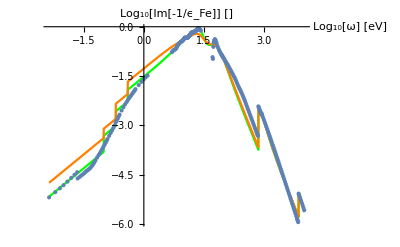

```mathematica
Show[{Plot[Log10[Sum["Ai" ELFM0[10^ω("JpereV")/("ℏ")/.SIcrustparams ,"νi","ωi"]HeavisideTheta[("JpereV")/("ℏ")10^ω-"ωedgei"]/.FeTotalparams[[i]],{i,Length[FeTotalparams]}]],{ω,(fFe@Domain)[[1,1]],(fFe@Domain)[[1,2]]},PlotStyle->Green,PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]] []"],Plot[Log10[Sum["Ai" ELFM0[10^ω("JpereV")/("ℏ")/.SIConstRepl ,"νi","ωi"]HeavisideTheta[("JpereV")/("ℏ")10^ω-"ωedgei"]/.FeTotalparamsExtrapolated[[i]],{i,Length[FeTotalparamsExtrapolated]}]],{ω,(fFe@Domain)[[1,1]],(fFe@Domain)[[1,2]]},PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotStyle->Orange,PlotLabel->"Log_10[Im[-1/ϵ_Fe]] [] - Extrapolated"],ListPlot[Log10[SortBy[ELFFeData,First]]]}]
```

#### Realized that the contribution from single phonon and elastic scattering a la Ziman are seperate and should be added. The Ziman is the room temperature dominant contribution and at Large T scales linear only from the single phonon contribution

```mathematica
ZimanFaberLin[params_] :=( (4 "m" ("e")^4 ("Z")^2)/(π ("ℏ")^3 ("ϵ0")^2)/.params)("nI""qF"/.params)NIntegrate[z^3 (1/((2"qF")^2  z^2 ϵRPA0[z])/.params)^2  ,{z,0,1} ]
```

```mathematica
νPhononMarderLinT[params_,T_] :=((4π("e")^2 "ne")/("ϵ0" "m")/.params)( (3 π "ϵ0")/(4π("e")^2"ℏ" ("vF")^2)/.params)("nI"/.params)(1/(4 ("qF")^4)/.params)(("ℏ")/(2 "M" cFe)/.params)(("kB" T)/("ℏ" cFe)/.params)^5 NIntegrate[z^4/(E^z-1) (((("e")^2 "Z")/("ϵ0"))/(((z"kB" T)/("ℏ" cFe))^2 ϵRPA0[1/(2"qF")((z"kB" T)/("ℏ" cFe))])/.params)^2  ,{z,0,2 ΘFe/T/.params} ]
```

```mathematica
ZimanFaberLin[SIcrustparams] + νPhononMarderLinT[SIcrustparams,273]
ZimanFaberLin[SIcoreparams] + νPhononMarderLinT[SIcoreparams,5400]
```

6.98464×10^16

8.20774×10^16

```mathematica
Plot[ZimanFaberLin[SIcoreparams] + νPhononMarderLinT[SIcoreparams,T],{T,273,5000}]
```

-Graphics-

```mathematica
Show[{Plot[ZimanFaberLin[SIcoreparams] + νPhononMarderLinT[SIcoreparams,T],{T,273,5500},PlotRange->{0,10^17}],ListPlot[νofT],Plot[ρ0 + dρdT  T/.νFit["BestFitParameters"],{T,0,5500}]}]
```

-Graphics-

#### Run Fe with rescaled collision rate

```mathematica
(*FeELOutputDict=EnergyLossTableAndInterFITTotalParams[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ"->2,"vχ"->2|>,FeTotalparams,True,"FeELOutputDictSI"]*)
```

Rescale according to Energy Loss notebook

```mathematica
FeTotalparamsExtrapolated[[5]]=RescaleAi[FeTotalparamsExtrapolated[[5]],0.75]
FeTotalparamsExtrapolated[[6]]=RescaleAi[FeTotalparamsExtrapolated[[6]],0.70]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.55522×10^17,Ai→0.00144809,ωedgei→1.09042×10^18}

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.23434×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}

```mathematica
FeELOutputDictExtrapolated=EnergyLossTableAndInterFITTotalParams[{2.5 10^5,2.5 10^10} ("JpereV")/("c")^2/.SIConstRepl,{2.5 10^-5,2.5 10^-2} "c" /.SIConstRepl,<|"mχ"->6,"vχ"->4|>,FeTotalparamsExtrapolated,True,"../ELandKappamin/compute energy loss/FeELOutputDictSIExtrapolated"]
```

1 of 24

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000994811 
Prefactor:	8.19529×10^15
dEdr:	8.15277×10^12

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000817081 
Prefactor:	6.19052×10^15
dEdr:	5.05816×10^12

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000512713 
Prefactor:	1.01998×10^17
dEdr:	5.22956×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	0.000158287 
Prefactor:	8.78553×10^17
dEdr:	1.39063×10^14

For mχ = 4.45×10^-31 , vχ = 7500.
L:	9.31827×10^-6 
Prefactor:	3.59493×10^18
dEdr:	3.34985×10^13

For mχ = 4.45×10^-31 , vχ = 7500.
L:	5.34951×10^-7 
Prefactor:	2.17433×10^18
dEdr:	1.16316×10^12

dEdr total: 2.39231×10^14

2 of 24

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00994709 
Prefactor:	8.19529×10^13
dEdr:	8.15193×10^11

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00816993 
Prefactor:	6.19052×10^13
dEdr:	5.05761×10^11

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00512674 
Prefactor:	1.01998×10^15
dEdr:	5.22916×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.00158282 
Prefactor:	8.78553×10^15
dEdr:	1.39059×10^13

For mχ = 4.45×10^-31 , vχ = 75000.
L:	0.0000931826 
Prefactor:	3.59493×10^16
dEdr:	3.34985×10^12

For mχ = 4.45×10^-31 , vχ = 75000.
L:	5.34951×10^-6 
Prefactor:	2.17433×10^16
dEdr:	1.16316×10^11

dEdr total: 2.39222×10^13

3 of 24

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0985476 
Prefactor:	8.19529×10^11
dEdr:	8.07625×10^10

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0808689 
Prefactor:	6.19052×10^11
dEdr:	5.00621×10^10

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0508923 
Prefactor:	1.01998×10^13
dEdr:	5.1909×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0157832 
Prefactor:	8.78553×10^13
dEdr:	1.38664×10^12

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.000931744 
Prefactor:	3.59493×10^14
dEdr:	3.34956×10^11

For mχ = 4.45×10^-31 , vχ = 750000.
L:	0.0000534954 
Prefactor:	2.17433×10^14
dEdr:	1.16317×10^10

dEdr total: 2.38314×10^12

4 of 24

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	1.0663 
Prefactor:	8.19529×10^9
dEdr:	8.73866×10^9

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.869994 
Prefactor:	6.19052×10^9
dEdr:	5.38571×10^9

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.54813 
Prefactor:	1.01998×10^11
dEdr:	5.5908×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.148458 
Prefactor:	8.78553×10^11
dEdr:	1.30429×10^11

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.00923603 
Prefactor:	3.59493×10^12
dEdr:	3.32029×10^10

For mχ = 4.45×10^-31 , vχ = 7.5×10^6
L:	0.000535227 
Prefactor:	2.17433×10^12
dEdr:	1.16376×10^9

dEdr total: 2.34828×10^11

5 of 24

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000834417 
Prefactor:	8.19529×10^15
dEdr:	6.83828×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000476199 
Prefactor:	6.19052×10^15
dEdr:	2.94792×10^11

For mχ = 4.45×10^-30 , vχ = 7500.
L:	0.0000301534 
Prefactor:	1.01998×10^17
dEdr:	3.07557×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	9.88494×10^-6 
Prefactor:	8.78553×10^17
dEdr:	8.68445×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	4.52159×10^-7 
Prefactor:	3.59493×10^18
dEdr:	1.62548×10^12

For mχ = 4.45×10^-30 , vχ = 7500.
L:	2.27868×10^-8 
Prefactor:	2.17433×10^18
dEdr:	4.9546×10^10

dEdr total: 1.44137×10^13

6 of 24

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000855663 
Prefactor:	8.19529×10^13
dEdr:	7.0124×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000485136 
Prefactor:	6.19052×10^13
dEdr:	3.00324×10^10

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.000305025 
Prefactor:	1.01998×10^15
dEdr:	3.11119×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	0.0000992067 
Prefactor:	8.78553×10^15
dEdr:	8.71583×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	4.52251×10^-6 
Prefactor:	3.59493×10^16
dEdr:	1.62581×10^11

For mχ = 4.45×10^-30 , vχ = 75000.
L:	2.27871×10^-7 
Prefactor:	2.17433×10^16
dEdr:	4.95467×10^9

dEdr total: 1.45039×10^12

7 of 24

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0278074 
Prefactor:	8.19529×10^11
dEdr:	2.2789×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0136269 
Prefactor:	6.19052×10^11
dEdr:	8.43573×10^9

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00650525 
Prefactor:	1.01998×10^13
dEdr:	6.6352×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.00134782 
Prefactor:	8.78553×10^13
dEdr:	1.18413×10^11

For mχ = 4.45×10^-30 , vχ = 750000.
L:	0.0000461536 
Prefactor:	3.59493×10^14
dEdr:	1.65919×10^10

For mχ = 4.45×10^-30 , vχ = 750000.
L:	2.28174×10^-6 
Prefactor:	2.17433×10^14
dEdr:	4.96125×10^8

dEdr total: 2.33078×10^11

8 of 24

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	1.32118 
Prefactor:	8.19529×10^9
dEdr:	1.08274×10^10

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	1.08144 
Prefactor:	6.19052×10^9
dEdr:	6.6947×10^9

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.706204 
Prefactor:	1.01998×10^11
dEdr:	7.20312×10^10

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.192263 
Prefactor:	8.78553×10^11
dEdr:	1.68913×10^11

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.00138043 
Prefactor:	3.59493×10^12
dEdr:	4.96255×10^9

For mχ = 4.45×10^-30 , vχ = 7.5×10^6
L:	0.000025843 
Prefactor:	2.17433×10^12
dEdr:	5.61913×10^7

dEdr total: 2.63485×10^11

9 of 24

For mχ = 4.45×10^-29 , vχ = 7500.
L:	8.72788×10^-7 
Prefactor:	8.19529×10^15
dEdr:	7.15275×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	4.82357×10^-7 
Prefactor:	6.19052×10^15
dEdr:	2.98604×10^9

For mχ = 4.45×10^-29 , vχ = 7500.
L:	3.04516×10^-7 
Prefactor:	1.01998×10^17
dEdr:	3.10599×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	1.00159×10^-7 
Prefactor:	8.78553×10^17
dEdr:	8.79953×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	4.52697×10^-9 
Prefactor:	3.59493×10^18
dEdr:	1.62742×10^10

For mχ = 4.45×10^-29 , vχ = 7500.
L:	2.26236×10^-10 
Prefactor:	2.17433×10^18
dEdr:	4.91913×10^8

dEdr total: 1.4596×10^11

10 of 24

For mχ = 4.45×10^-29 , vχ = 75000.
L:	0.0000335339 
Prefactor:	8.19529×10^13
dEdr:	2.7482×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	0.0000142237 
Prefactor:	6.19052×10^13
dEdr:	8.80519×10^8

For mχ = 4.45×10^-29 , vχ = 75000.
L:	6.75643×10^-6 
Prefactor:	1.01998×10^15
dEdr:	6.8914×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	1.39123×10^-6 
Prefactor:	8.78553×10^15
dEdr:	1.22227×10^10

For mχ = 4.45×10^-29 , vχ = 75000.
L:	4.62374×10^-8 
Prefactor:	3.59493×10^16
dEdr:	1.6622×10^9

For mχ = 4.45×10^-29 , vχ = 75000.
L:	2.26546×10^-9 
Prefactor:	2.17433×10^16
dEdr:	4.92586×10^7

dEdr total: 2.44542×10^10

11 of 24

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.0216803 
Prefactor:	8.19529×10^11
dEdr:	1.77677×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.00916827 
Prefactor:	6.19052×10^11
dEdr:	5.67563×10^9

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.00367565 
Prefactor:	1.01998×10^13
dEdr:	3.74908×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	0.000399326 
Prefactor:	8.78553×10^13
dEdr:	3.50829×10^10

For mχ = 4.45×10^-29 , vχ = 750000.
L:	1.42982×10^-6 
Prefactor:	3.59493×10^14
dEdr:	5.14012×10^8

For mχ = 4.45×10^-29 , vχ = 750000.
L:	2.5752×10^-8 
Prefactor:	2.17433×10^14
dEdr:	5.59934×10^6

dEdr total: 9.65366×10^10

12 of 24

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	1.31193 
Prefactor:	8.19529×10^9
dEdr:	1.07516×10^10

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	1.07394 
Prefactor:	6.19052×10^9
dEdr:	6.64826×10^9

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.700468 
Prefactor:	1.01998×10^11
dEdr:	7.14461×10^10

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.188806 
Prefactor:	8.78553×10^11
dEdr:	1.65876×10^11

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	0.000965625 
Prefactor:	3.59493×10^12
dEdr:	3.47136×10^9

For mχ = 4.45×10^-29 , vχ = 7.5×10^6
L:	3.35365×10^-6 
Prefactor:	2.17433×10^12
dEdr:	7.29196×10^6

dEdr total: 2.582×10^11

13 of 24

For mχ = 4.45×10^-28 , vχ = 7500.
L:	3.36223×10^-8 
Prefactor:	8.19529×10^15
dEdr:	2.75545×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	1.42358×10^-8 
Prefactor:	6.19052×10^15
dEdr:	8.81271×10^7

For mχ = 4.45×10^-28 , vχ = 7500.
L:	6.76134×10^-9 
Prefactor:	1.01998×10^17
dEdr:	6.89641×10^8

For mχ = 4.45×10^-28 , vχ = 7500.
L:	1.39194×10^-9 
Prefactor:	8.78553×10^17
dEdr:	1.2229×10^9

For mχ = 4.45×10^-28 , vχ = 7500.
L:	4.62488×10^-11 
Prefactor:	3.59493×10^18
dEdr:	1.66261×10^8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 2.26593×10^-12 and 3.85729×10^-18 for the integral and error estimates.

For mχ = 4.45×10^-28 , vχ = 7500.
L:	2.26593×10^-12 
Prefactor:	2.17433×10^18
dEdr:	4.92687×10^6

dEdr total: 2.4474×10^9

14 of 24

For mχ = 4.45×10^-28 , vχ = 75000.
L:	0.0000251849 
Prefactor:	8.19529×10^13
dEdr:	2.06397×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	9.54984×10^-6 
Prefactor:	6.19052×10^13
dEdr:	5.91184×10^8

For mχ = 4.45×10^-28 , vχ = 75000.
L:	3.78241×10^-6 
Prefactor:	1.01998×10^15
dEdr:	3.85797×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	4.04044×10^-7 
Prefactor:	8.78553×10^15
dEdr:	3.54974×10^9

For mχ = 4.45×10^-28 , vχ = 75000.
L:	1.43104×10^-9 
Prefactor:	3.59493×10^16
dEdr:	5.14449×10^7

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 2.57584×10^-11 and 2.72559×10^-17 for the integral and error estimates.

For mχ = 4.45×10^-28 , vχ = 75000.
L:	2.57584×10^-11 
Prefactor:	2.17433×10^16
dEdr:	560074.

dEdr total: 1.01149×10^10

15 of 24

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.0216203 
Prefactor:	8.19529×10^11
dEdr:	1.77184×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.0091248 
Prefactor:	6.19052×10^11
dEdr:	5.64872×10^9

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.00364796 
Prefactor:	1.01998×10^13
dEdr:	3.72084×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	0.000389869 
Prefactor:	8.78553×10^13
dEdr:	3.42521×10^10

For mχ = 4.45×10^-28 , vχ = 750000.
L:	9.82619×10^-7 
Prefactor:	3.59493×10^14
dEdr:	3.53245×10^8

For mχ = 4.45×10^-28 , vχ = 750000.
L:	3.35673×10^-9 
Prefactor:	2.17433×10^14
dEdr:	729865.

dEdr total: 9.51815×10^10

16 of 24

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	1.31184 
Prefactor:	8.19529×10^9
dEdr:	1.07509×10^10

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	1.07387 
Prefactor:	6.19052×10^9
dEdr:	6.6478×10^9

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.700411 
Prefactor:	1.01998×10^11
dEdr:	7.14404×10^10

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.188772 
Prefactor:	8.78553×10^11
dEdr:	1.65846×10^11

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	0.00096154 
Prefactor:	3.59493×10^12
dEdr:	3.45667×10^9

For mχ = 4.45×10^-28 , vχ = 7.5×10^6
L:	3.13094×10^-6 
Prefactor:	2.17433×10^12
dEdr:	6.80769×10^6

dEdr total: 2.58148×10^11

17 of 24

For mχ = 4.45×10^-27 , vχ = 7500.
L:	2.5229×10^-8 
Prefactor:	8.19529×10^15
dEdr:	2.06759×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	9.5547×10^-9 
Prefactor:	6.19052×10^15
dEdr:	5.91485×10^7

For mχ = 4.45×10^-27 , vχ = 7500.
L:	3.78369×10^-9 
Prefactor:	1.01998×10^17
dEdr:	3.85927×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	4.04095×10^-10 
Prefactor:	8.78553×10^17
dEdr:	3.55019×10^8

For mχ = 4.45×10^-27 , vχ = 7500.
L:	1.43105×10^-12 
Prefactor:	3.59493×10^18
dEdr:	5.14453×10^6

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00006}. NIntegrate obtained 2.57585×10^-14 and 2.77077×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-27 , vχ = 7500.
L:	2.57585×10^-14 
Prefactor:	2.17433×10^18
dEdr:	56007.5

dEdr total: 1.01205×10^9

18 of 24

For mχ = 4.45×10^-27 , vχ = 75000.
L:	0.0000251014 
Prefactor:	8.19529×10^13
dEdr:	2.05713×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	9.5031×10^-6 
Prefactor:	6.19052×10^13
dEdr:	5.88291×10^8

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.75267×10^-6 
Prefactor:	1.01998×10^15
dEdr:	3.82764×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.94171×10^-7 
Prefactor:	8.78553×10^15
dEdr:	3.463×10^9

For mχ = 4.45×10^-27 , vχ = 75000.
L:	9.8287×10^-10 
Prefactor:	3.59493×10^16
dEdr:	3.53335×10^7

For mχ = 4.45×10^-27 , vχ = 75000.
L:	3.35678×10^-12 
Prefactor:	2.17433×10^16
dEdr:	72987.5

dEdr total: 9.97146×10^9

19 of 24

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.0216197 
Prefactor:	8.19529×10^11
dEdr:	1.77179×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00912436 
Prefactor:	6.19052×10^11
dEdr:	5.64845×10^9

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.00364768 
Prefactor:	1.01998×10^13
dEdr:	3.72055×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	0.000389774 
Prefactor:	8.78553×10^13
dEdr:	3.42437×10^10

For mχ = 4.45×10^-27 , vχ = 750000.
L:	9.78146×10^-7 
Prefactor:	3.59493×10^14
dEdr:	3.51637×10^8

For mχ = 4.45×10^-27 , vχ = 750000.
L:	3.13274×10^-9 
Prefactor:	2.17433×10^14
dEdr:	681161.

dEdr total: 9.5168×10^10

20 of 24

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	1.31184 
Prefactor:	8.19529×10^9
dEdr:	1.07509×10^10

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	1.07387 
Prefactor:	6.19052×10^9
dEdr:	6.6478×10^9

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.700411 
Prefactor:	1.01998×10^11
dEdr:	7.14403×10^10

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.188771 
Prefactor:	8.78553×10^11
dEdr:	1.65846×10^11

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	0.000961499 
Prefactor:	3.59493×10^12
dEdr:	3.45652×10^9

For mχ = 4.45×10^-27 , vχ = 7.5×10^6
L:	3.12871×10^-6 
Prefactor:	2.17433×10^12
dEdr:	6.80285×10^6

dEdr total: 2.58148×10^11

21 of 24

For mχ = 4.45×10^-26 , vχ = 7500.
L:	2.51451×10^-8 
Prefactor:	8.19529×10^15
dEdr:	2.06071×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	9.50789×10^-9 
Prefactor:	6.19052×10^15
dEdr:	5.88588×10^7

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.75391×10^-9 
Prefactor:	1.01998×10^17
dEdr:	3.8289×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.94216×10^-10 
Prefactor:	8.78553×10^17
dEdr:	3.4634×10^8

For mχ = 4.45×10^-26 , vχ = 7500.
L:	9.82872×10^-13 
Prefactor:	3.59493×10^18
dEdr:	3.53336×10^6

For mχ = 4.45×10^-26 , vχ = 7500.
L:	3.35678×10^-15 
Prefactor:	2.17433×10^18
dEdr:	7298.75

dEdr total: 9.97701×10^8

22 of 24

For mχ = 4.45×10^-26 , vχ = 75000.
L:	0.0000251005 
Prefactor:	8.19529×10^13
dEdr:	2.05706×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	9.50263×10^-6 
Prefactor:	6.19052×10^13
dEdr:	5.88262×10^8

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.75237×10^-6 
Prefactor:	1.01998×10^15
dEdr:	3.82733×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.94072×10^-7 
Prefactor:	8.78553×10^15
dEdr:	3.46213×10^9

For mχ = 4.45×10^-26 , vχ = 75000.
L:	9.78388×10^-10 
Prefactor:	3.59493×10^16
dEdr:	3.51724×10^7

For mχ = 4.45×10^-26 , vχ = 75000.
L:	3.13276×10^-12 
Prefactor:	2.17433×10^16
dEdr:	68116.6

dEdr total: 9.97003×10^9

23 of 24

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.0216196 
Prefactor:	8.19529×10^11
dEdr:	1.77179×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00912436 
Prefactor:	6.19052×10^11
dEdr:	5.64845×10^9

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.00364768 
Prefactor:	1.01998×10^13
dEdr:	3.72055×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	0.000389773 
Prefactor:	8.78553×10^13
dEdr:	3.42437×10^10

For mχ = 4.45×10^-26 , vχ = 750000.
L:	9.78102×10^-7 
Prefactor:	3.59493×10^14
dEdr:	3.51621×10^8

For mχ = 4.45×10^-26 , vχ = 750000.
L:	3.1305×10^-9 
Prefactor:	2.17433×10^14
dEdr:	680674.

dEdr total: 9.51678×10^10

24 of 24

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	1.31184 
Prefactor:	8.19529×10^9
dEdr:	1.07509×10^10

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	1.07387 
Prefactor:	6.19052×10^9
dEdr:	6.6478×10^9

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.700411 
Prefactor:	1.01998×10^11
dEdr:	7.14403×10^10

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.188771 
Prefactor:	8.78553×10^11
dEdr:	1.65846×10^11

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	0.000961499 
Prefactor:	3.59493×10^12
dEdr:	3.45652×10^9

For mχ = 4.45×10^-26 , vχ = 7.5×10^6
L:	3.12869×10^-6 
Prefactor:	2.17433×10^12
dEdr:	6.8028×10^6

dEdr total: 2.58148×10^11

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-31,4.45×10^-31,4.45×10^-31,4.45×10^-31},{4.45×10^-30,4.45×10^-30,4.45×10^-30,4.45×10^-30},{4.45×10^-29,4.45×10^-29,4.45×10^-29,4.45×10^-29},{4.45×10^-28,4.45×10^-28,4.45×10^-28,4.45×10^-28},{4.45×10^-27,4.45×10^-27,4.45×10^-27,4.45×10^-27},{4.45×10^-26,4.45×10^-26,4.45×10^-26,4.45×10^-26}},vχMesh→{{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6}},EnergyLossMesh→{{2.39231×10^14,2.39222×10^13,2.38314×10^12,2.34828×10^11},{1.44137×10^13,1.45039×10^12,2.33078×10^11,2.63485×10^11},{1.4596×10^11,2.44542×10^10,9.65366×10^10,2.582×10^11},{2.4474×10^9,1.01149×10^10,9.51815×10^10,2.58148×10^11},{1.01205×10^9,9.97146×10^9,9.5168×10^10,2.58148×10^11},{9.97701×10^8,9.97003×10^9,9.51678×10^10,2.58148×10^11}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→3.22338×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→2.37219×10^16,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→3.49108×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→1.07806×10^17,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.55522×10^17,Ai→0.00144809,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.23434×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}},fname→../ELandKappamin/compute energy loss/FeELOutputDictSIExtrapolated,kinlist→<|mχ→{4.45×10^-31,4.45×10^-30,4.45×10^-29,4.45×10^-28,4.45×10^-27,4.45×10^-26},vχ→{7500.,75000.,750000.,7.5×10^6}|>,meshdims→<|mχ→6,vχ→4|>,timesMesh→{{23.0342,28.2288,27.2185,56.0762},{23.5636,26.0271,26.6887,61.3101},{29.3346,27.0781,32.1591,54.5953},{31.1575,31.7666,30.5913,56.0506},{33.3714,31.3227,28.3153,54.5415},{29.5997,28.1011,27.3544,54.9755}},totalTime→852.462|>

#### Plot Iron with rescaled collision rate

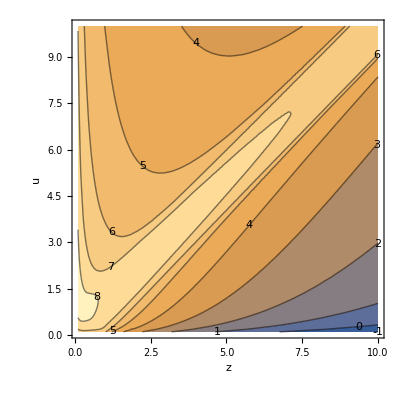

```mathematica
Utilities`ContourTotalParams[FeELOutputDictExtrapolated[["fitparams"]]]
```

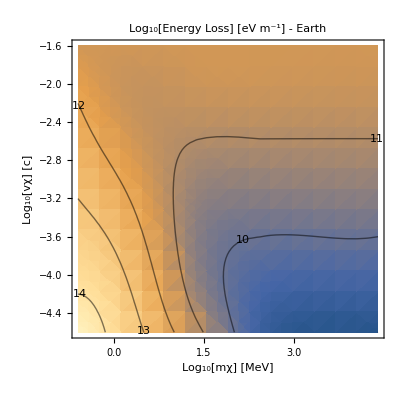

```mathematica
EnergyLoss`PlotEL[FeELOutputDictExtrapolated]
```

#### Rescale number density and extrapolate to the core

```mathematica
((1+ 2/3)"nI"/.SIcrustparams)/("nI"/.SIcoreparams)
```

1.